```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Needs["shane`"]
```

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs/mc-2013"];
```

```mathematica
fode = Import["results-2/fode.m"]
```

{genCounts→{23,49,28,11,29,50,4,24,9,12,10,5,10,30,12,6,15,32,5,9},evalCounts→{276,588,336,132,348,600,48,288,108,144,120,60,120,360,144,72,180,384,60,108},wallClockTimes→{45.08,90.13,52.57,20.94,54.22,92.29,7.81,44.89,17.04,22.62,18.91,9.66,18.81,57.94,23.78,12.09,28.58,59.54,9.69,17.14},success→{1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
bullet = Import["results-2/bullet.m"]
```

{genCounts→{13,10,23,39,11,25,27,24,39,8,25,1,20,33,23,20,18,49,13,28},evalCounts→{156,120,276,468,132,300,324,288,468,96,300,12,240,396,276,240,216,588,156,336},wallClockTimes→{30.06,23.2,52.78,92.23,25.66,58.32,62.09,55.11,92.32,18.74,57.11,2.77,46.08,81.19,56.91,48.51,44.01,117.56,30.07,63.95},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
f2b = Import["results-2/f2b2.m"]
```

{genCounts→{2,1,1,5,1,1,1,1,5,1,1,1,3,1,1,1,12,5,1},evalCounts→{24,12,12,60,12,12,12,12,60,12,12,12,36,12,12,12,144,60,12},wallClockTimes→{9.15,4.91,4.91,23.48,4.95,4.92,4.93,4.9,22.99,4.91,4.92,4.91,16.2,5.16,5.22,5.04,53.75,22.96,4.92},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
standardErrorOfMean[list_] := Module[{n,s},s=StandardDeviation[list];
n=Length[list];
s/n^(1/2)]
```

```mathematica
meanAndDev[lists_, key_] := Map[{Mean[key /. #], standardErrorOfMean[key /. #]}&, lists]
```

```mathematica
show[lists_, key_] := Module[{},
ErrorListPlot[meanAndDev[lists, key], PlotRange -> All, AxesOrigin -> {0, 0}]]
```

```mathematica
meanAndDev[lists, genCounts]
```

{{373/20,(11 √(611/19))/20},{449/20,(3 √(5771/19))/20},{45/19,(√1315)/57}}

```mathematica
lists = {fode, bullet, f2b};
```

```mathematica
lists1 = Map[Import["results-1/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{15,5,20,50,50,15,10,14,14,36,20,22,5,7},evalCounts→{180,60,240,600,600,180,120,168,168,432,240,264,60,84},wallClockTimes→{30.06,10.14,39.2,95.26,101.12,32.92,19.39,27.3,27.49,68.61,39.18,41.72,10.23,14.74},success→{1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{28,24,7,8,10,18,1,1,18,13,36,27,27,36},evalCounts→{336,288,84,96,120,216,12,12,216,156,432,324,324,432},wallClockTimes→{86.05,59.13,16.57,18.6,23.54,48.13,2.81,2.71,43.26,32.66,88.23,60.29,66.56,84.45},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{genCounts→{1,1,5,1,1,1,1,1,1,1,1,1},evalCounts→{12,12,60,12,12,12,12,12,12,12,12,12},wallClockTimes→{4.92,5.25,23.21,4.99,5.06,5.02,5.11,5.05,5.,5.16,4.99,4.97},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

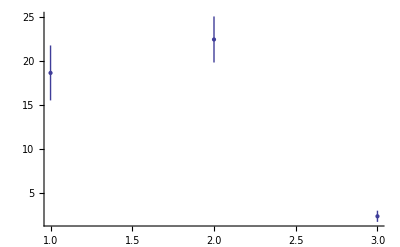

```mathematica
show[lists, genCounts]
```

```mathematica
show[lists_, key_, opts:OptionsPattern[]] := ErrorListPlot[meanAndDev[lists, key], AxesOrigin -> {.8, 0},opts,PlotRange->Full,(*PlotRange -> {Automatic, {0, 50}}, *)AxesLabel -> {"Physics/Vehicle", key}, Ticks -> {Transpose[{{1,2,3},{"FODE", "Bullet", "FODE->Bullet"}}], Automatic}, Joined -> True]
```

```mathematica
checkSignificance[lists_, key_] := TableForm[{{"FODE vs. Bullet", MannWhitneyTest[{key /. lists[[1]] , key /. lists[[2]]}]},
{"Bullet vs FODE -> Bullet", MannWhitneyTest[{Pick[(key /. lists[[1]]), Map[IntegerPart,success /. lists[[1]]], 1 ] + (key /. lists[[3]]) , key /. lists[[2]]}]}}]
```

```mathematica
checkSignificance[lists, genCounts]
```

FODE vs. Bullet | 0.218211
Bullet vs FODE -> Bullet | 0.304804

```mathematica
checkSignificance[lists, evalCounts]
```

FODE vs. Bullet | 0.218211
Bullet vs FODE -> Bullet | 0.304804

```mathematica
checkSignificance[lists, wallClockTimes]
```

FODE vs. Bullet | 0.0222699
Bullet vs FODE -> Bullet | 0.181996

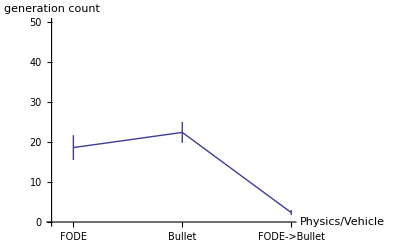

```mathematica
show[lists,genCounts, PlotRange -> {Automatic,{0, 50}}, AxesLabel -> {"Physics/Vehicle", "generation count"} ]
```

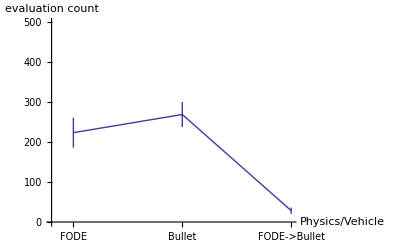

```mathematica
show[lists,evalCounts, PlotRange -> {Automatic, {0, 500}}, AxesLabel -> {"Physics/Vehicle", "evaluation count"} ]
```

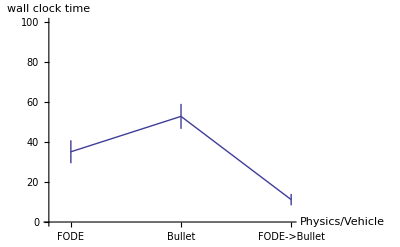

```mathematica
show[lists,wallClockTimes, PlotRange -> {Automatic, {0, 100}}, AxesLabel -> {"Physics/Vehicle",  "wall clock time"}]
```

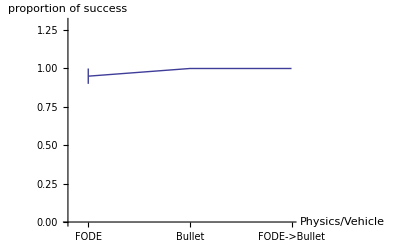

```mathematica
show[lists,success, PlotRange -> {Automatic, {0, 1.3}}, AxesLabel -> {"Physics/Vehicle", "proportion of success"}]
```

```mathematica
showAll[lists_] := GraphicsGrid[{{show[lists,genCounts, PlotRange -> {Automatic,{0, 50}}, AxesLabel -> {"Physics/Vehicle", "generation count"} ],
show[lists,evalCounts, PlotRange -> {Automatic, {0, 500}}, AxesLabel -> {"Physics/Vehicle", "evaluation count"} ]},
{show[lists,wallClockTimes, PlotRange -> {Automatic, {0, 100}}, AxesLabel -> {"Physics/Vehicle",  "wall clock time"}],
show[lists,success, PlotRange -> {Automatic, {0, 1.3}}, AxesLabel -> {"Physics/Vehicle", "proportion of success"}]}}]
```

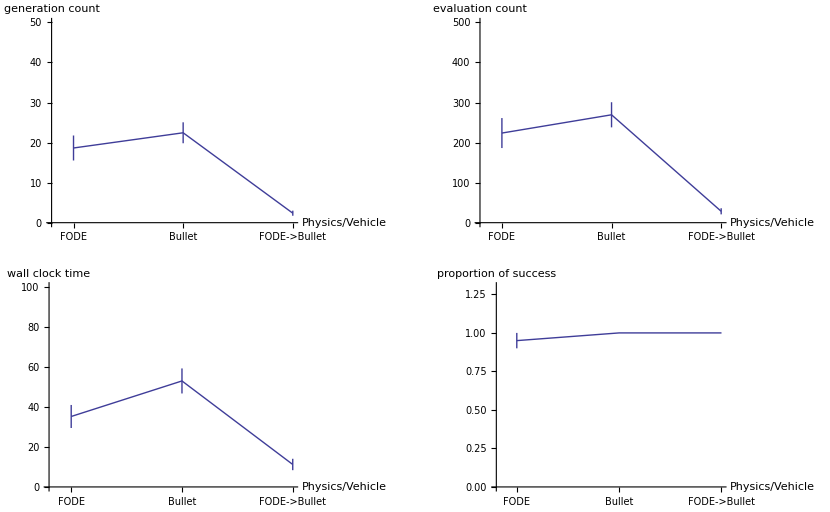

```mathematica
showAll[lists]
```

```mathematica
Export["results.pdf",%,"PDF", ImageSize -> 72 {7, 7}]
```

results.pdf

```mathematica
SystemOpen["results.pdf"]
```

```mathematica
SystemOpen["results.pdf"]
```

```mathematica
SystemOpen["results.pdf"]
```

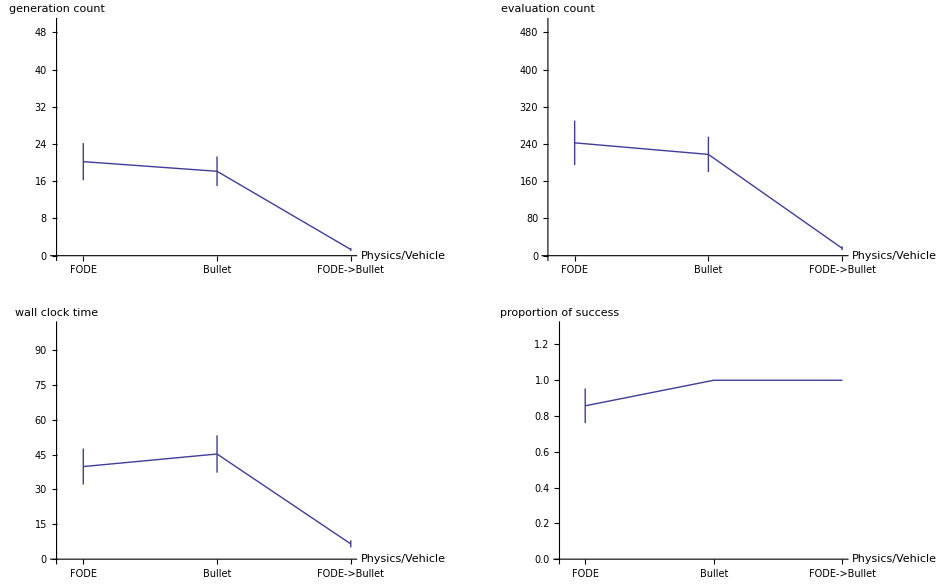

```mathematica
showAll[lists1]
```

```mathematica
Export["results.pdf", %]
```

results.pdf

```mathematica
lists3 = Map[Import["results-3/"<> # <>".m"]&, {"fode", "bullet", "f2b"}]
```

{{genCounts→{15,17,24,36,12,20,10,26,23,8,30,10,16,43,5,5,50,50,11,24},evalCounts→{180,204,288,432,144,240,120,312,276,96,360,120,192,516,60,60,600,600,132,288},wallClockTimes→{35.05,33.31,53.8,66.4,23.12,38.08,19.57,49.03,44.76,15.51,55.34,20.86,30.66,82.94,10.41,10.36,95.85,96.26,26.22,46.71},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.}},{genCounts→{50,39,50,23,50,50,50,50,16,22,32,33,50,50,50,34,50,29,50,50},evalCounts→{600,468,600,276,600,600,600,600,192,264,384,396,600,600,600,408,600,348,600,600},wallClockTimes→{178.68,118.12,165.39,61.63,130.99,131.8,132.64,131.83,37.36,51.26,74.36,93.19,126.87,143.94,153.89,84.07,157.05,74.13,150.49,148.75},success→{0.,1.,0.,1.,1.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,1.,0.,1.,0.,0.}},{genCounts→{1,1,3,1,1,2,2,2,8,1,1,6,1,1,1,14,1,3},evalCounts→{12,12,36,12,12,24,24,24,96,12,12,72,12,12,12,168,12,36},wallClockTimes→{5.96,5.04,15.71,4.93,4.93,9.56,9.59,9.38,36.28,4.9,4.87,27.52,4.97,5.11,4.99,65.79,7.47,14.85},success→{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
checkSignificance[lists3, genCounts]
```

FODE vs. Bullet | 0.000130302
Bullet vs FODE -> Bullet | 0.0000215115

```mathematica
checkSignificance[lists3, evalCounts]
```

FODE vs. Bullet | 0.000130302
Bullet vs FODE -> Bullet | 0.0000215115

```mathematica
checkSignificance[lists3, wallClockTimes]
```

FODE vs. Bullet | 3.98736×10^-6
Bullet vs FODE -> Bullet | 0.0000141554

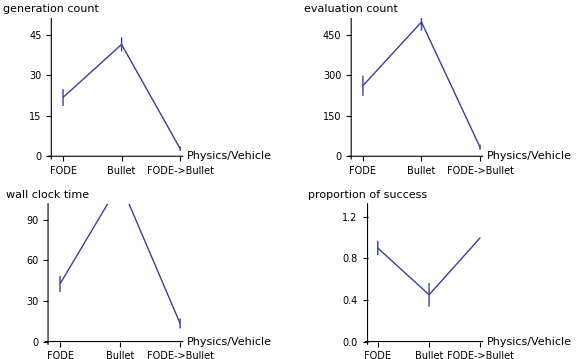

```mathematica
showAll[lists3]
```